## KERNEL-DOCS

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## Data Structures

```mathematica
data1={{{0,{{2,2},{4,4},{0,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}};
data2={{{0,{2+I,4+4I,4I}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}};
```

```mathematica
data1/.dat:pnt:>"POINT"
```

{{{0,{POINT,POINT,POINT}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

```mathematica
data1/.dat:pts:>"POINT-LIST"
```

{{{0,POINTLIST},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

```mathematica
data1/.dat:nls:>"NUMBER-LIST"
data2/.dat:nls:>"NUMBER-LIST"
```

{{{0,{NUMBER-LIST,NUMBER-LIST,NUMBER-LIST}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{{{0,NUMBER-LIST},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

```mathematica
data1/.dat:typ:>"D"
```

{{D,{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

```mathematica
data1/.dat:face:>"E"
```

{{{0,{{2,2},{4,4},{0,4}}},E},{GrayLevel[0],1,0.0125,2 π,2 π}}

```mathematica
data1/.dat:edge:>"F"
```

{{{0,{{2,2},{4,4},{0,4}}},{RGBColor[1, 0, 0],1}},F}

```mathematica
data1/.dat:clr:>"G"
```

{G,{GrayLevel[0],1,0.0125,2 π,2 π}}

```mathematica
data1/.dat:edg:>"H"
```

H

```mathematica
{gCircle[],gCircle[],gPoint[],gLine[]}/.edg:>"J"
```

{J,J,J,J}

## Geometric Objects

### Euclidean

#### POINT

```mathematica
POINT
```

0

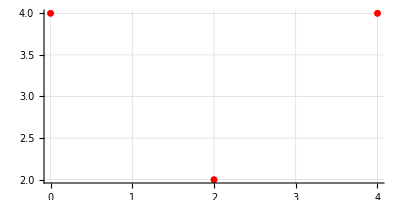

```mathematica
newGeo[{POINT,{{2,2},{4,4},{0,4}}}];
newGeo[{POINT,{{2,2},{4,4},{0,4}}}]//toGL;
newGeo[{POINT,{{2,2},{4,4},{0,4}}}]//toGL//gr1
```

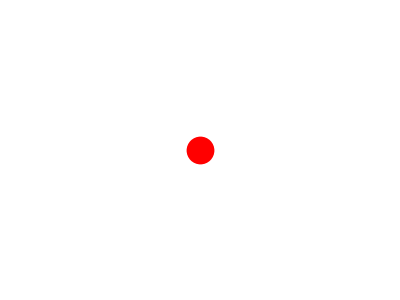

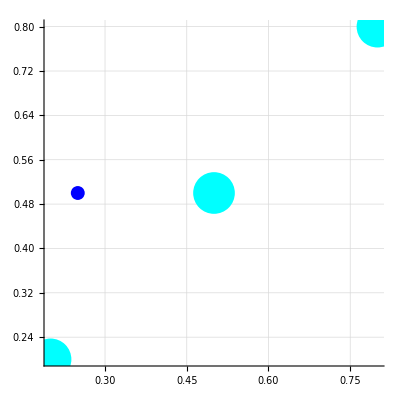

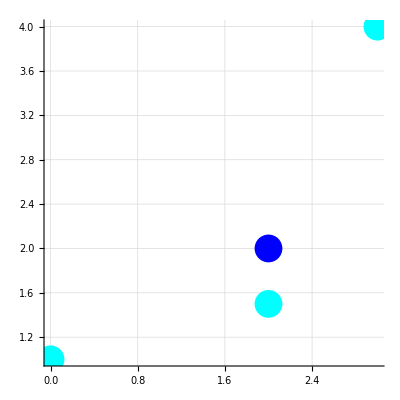

```mathematica
gPoint[PointSize->0.05]//toGL//gr
Show[
gPoint[{0.25,0.5},Color->Blue,PointSize->0.025]//toGL//gr1 ,
gPoint[{{0.2,0.2},{0.5,0.5},{0.8,0.8}},Color->Cyan,PointSize->0.075]//toGL//gr1
]
Show[
gPoint[2+2I,Color->Blue,PointSize->0.05]//toGL//gr1,
gPoint[{I,2+1.5I,3+4I},PointSize->0.05,Color->Cyan]//toGL//gr1
]
```

#### POLYGON

{{{1,{{2,2},{4,4},{0,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}],Polygon[…]}}

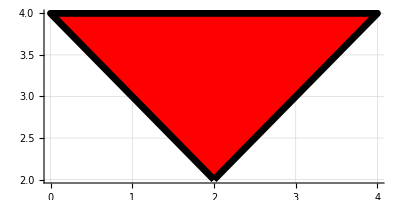

```mathematica
newGeo[{1,{{2,2},{4,4},{0,4}}}]
newGeo[{1,{{2,2},{4,4},{0,4}}}]//toGL
newGeo[{1,{{2,2},{4,4},{0,4}}}]//toGL//gr1
```

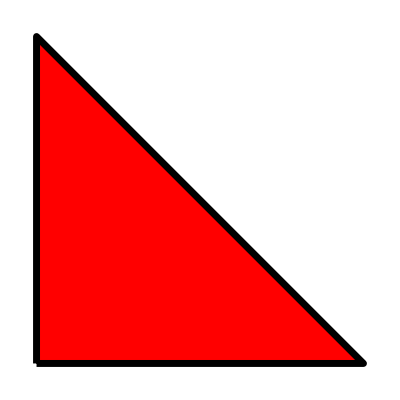

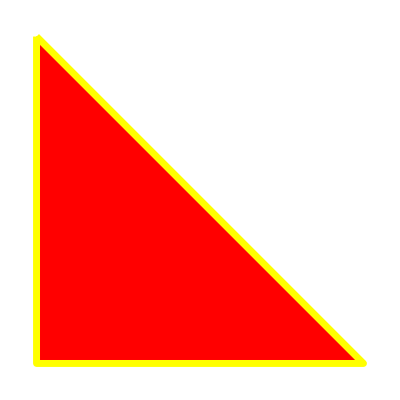

```mathematica
gPolygon[{{0,0},{1,0},{0,1}}]//toGL//gr
gPolygon[EdgeColor->Yellow]//toGL//gr
```

#### CIRCLE

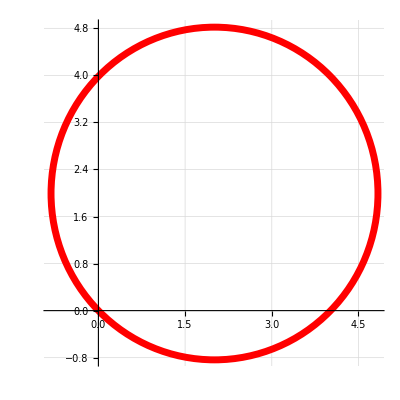

```mathematica
CIRCLE;
FACE;
EDGE;
newGeo[{CIRCLE,{{2,2},{4,4}}}]//TreeForm;
cCircle[{0,0},1]//toGL//gr1;
newGeo[{CIRCLE,{{2,2},{4,4}}}];
newGeo[{2,{{2,2},{4,4}}}]//toGL//gr1;
{{{2,{{2,2},{4,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}//toGL//gr1
```

```mathematica
newGeo[{CIRCLE,{{2,2},{4,4}}}];
newGeo[{CIRCLE,{{2,2},{4,4}}}]//toGL;
newGeo[{CIRCLE,{{2,2},{4,4}}}]//toGL//gr1
```

-Graphics-

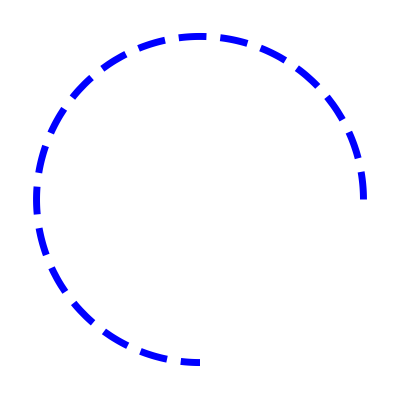

```mathematica
gCircle[2+2I,2 √2];
gCircle[2+2I,2 √2]//toGL;
gCircle[2+2I,2 √2,Color->Blue]//toGL//gr1;
gCircle[I,Color->Gray]//toGL//gr1;
gCircle[{0,1},1,Color->Green]//toGL//gr1;
gCircle[{6,6},1,0,3/2Pi,Color->Blue, Thickness->0.0125,Dashing->{.05,.025}]//toGL//gr
```

```mathematica
Options[gCircle]
```

{Color→RGBColor[1, 0, 0],Opacity→1,Thickness→0.0125,Dashing→{2 π,2 π}}

#### LINE

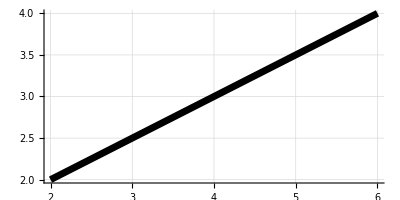

```mathematica
newGeo[{3,{{2,2},{4,4}}}];
newGeo[{3,{{2,2},{4,5}}}]//toGL;
newGeo[{3,{{2,2},{4,4}}}]//toGL//gr1;

fig1:=newGeo[{3,{{2,2},{6,4}}}];
fig1//toGL//gr1
```

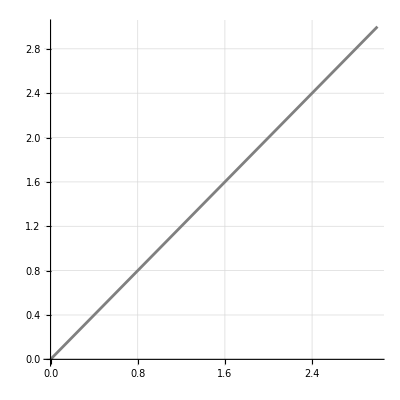

```mathematica
gLine[{2,2},{6,4},Color->Gray, Thickness->0.005]//toGL//gr1;
gLine[I,Color->Gray]//toGL//gr1;
gLine[{0,0},{3,3},Color->Gray, Thickness->0.005]//toGL//gr1
```

#### DISK

{{{4,{{2,2},{4,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}],Disk[{2,2},2 √2]}}

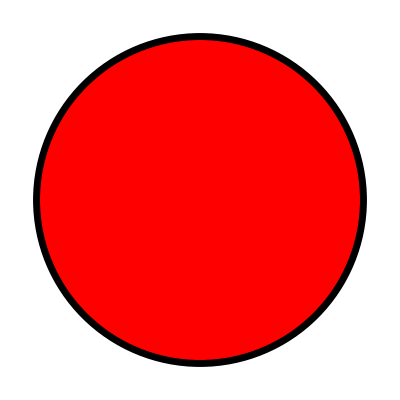

```mathematica
newGeo[{4,{{2,2},{4,4}}}]
newGeo[{4,{{2,2},{4,4}}}]//toGL
newGeo[{4,{{2,2},{4,4}}}]//toGL//gr
```

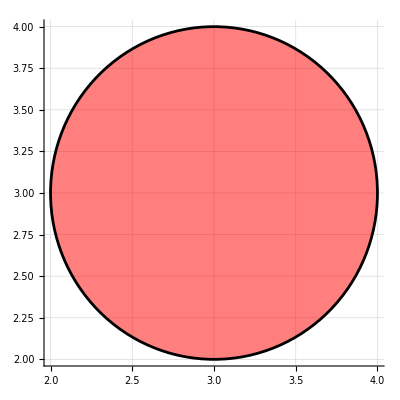

```mathematica
gDisk[2+2I,2 √2];
gDisk[2+2I,2 √2]//toGL//gr;
gDisk[2+2I,2 √2,FaceColor->Blue]//toGL//gr1;
gDisk[I,FaceColor->Gray]//toGL//gr1;
gDisk[{0,1},1,FaceColor->Green]//toGL//gr1;
gDisk[{3,3},FaceColor->Red, FaceOpacity->0.5,Thickness->0.005]//toGL//gr1
```

### Hyperbolic Upper Half-plane Model

```mathematica
Manipulate[
gHLineHP[p,q,Thickness->0.0075,Color->Green]//toGL//gr1
,
{{p,{0.6,0.2}},{-1,-1},{2,2},{0.1,0.1},Locator},
{{q,{0.4,0.4}},{-1,-1},{2,2},{0.1,0.1},Locator}
]
```

### Hyperbolic Poincaré Disk Model

#### HYPERBOLIC LINE

```mathematica
{
gPoint[{0.6,0.2},Color->Blue,PointSize->0.035],
gPoint[{0.4,0.4},Color->Blue,PointSize->0.035],
gPoint[{1.5,0.5},Color->Red],
gPoint[{1.25,1.25},Color->Red],
gPoint[{1.05,0.35},Color->Black,PointSize->0.025],
gPoint[{0.825,0.825},Color->Black,PointSize->0.025],
HalfLine[{{1.05,0.35},{0.5,2.0}}],
HalfLine[{{0.825,0.825},{1.5,0.15}}],
gCircle[{0.925,0.725},0.6174544517614234,ArcTan[0.6-0.925,0.2-0.725],ArcTan[0.4-0.925,0.4-0.725],Thickness->0.0125,Color->Red],gCircle[{0.925,0.725},0.6174544517614234,Thickness->0.0025,Color->Blue]
}//toGL//grD
```

-Graphics-

```mathematica
Manipulate[
gHLinePD[p,q,Thickness->0.0075,Color->Blue]//toGL//grD
,
{{p,{0.6,0.2}},{-1,-1},{2,2},{0.1,0.1},Locator},
{{q,{0.4,0.4}},{-1,-1},{2,2},{0.1,0.1},Locator}
]
```

## Transformations

### TRANSLATION

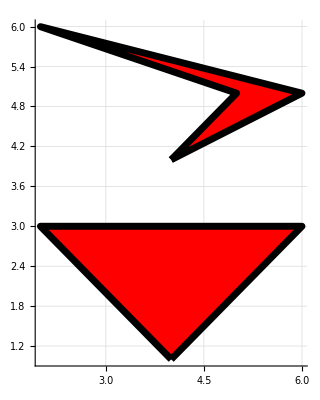

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
tra3[fig12,{2,-1}]//toGL//gr1
```

### ROTATION

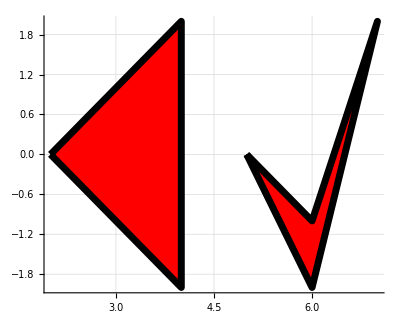

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
rot3[fig12,{3/2 Pi,{1,1}}]//toGL//gr1
```

### REFLECTION

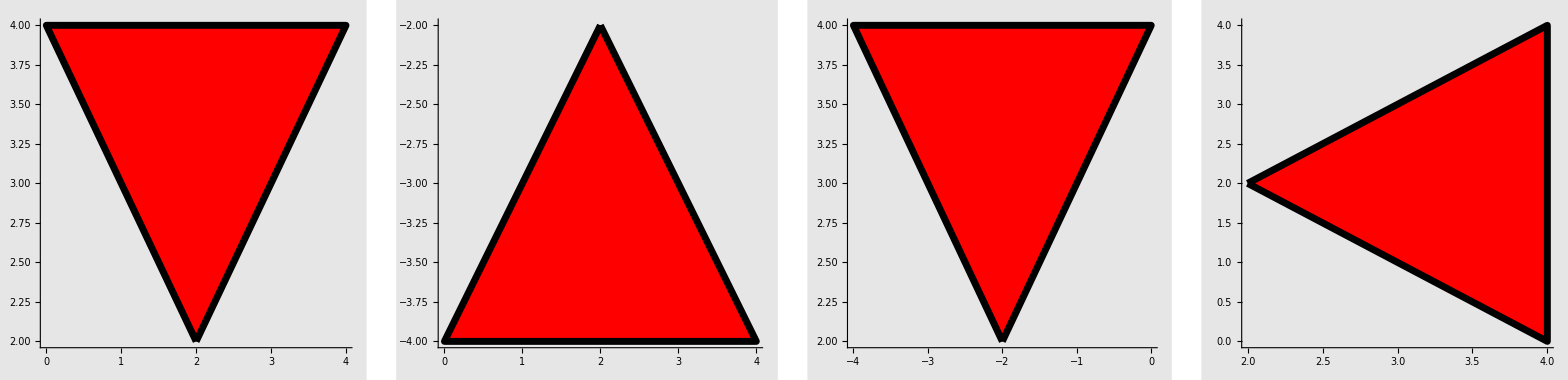

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
GraphicsRow[
{fig1//toGL//gr2,
ref3[fig1,{{0,1},{0,0}}]//toGL//gr2 (* Reflection in X-axis *),
ref3[fig1,{{1,0},{0,0}}]//toGL//gr2 (* Reflection in Y-axis *),
ref3[fig1,{{-1,1},{0,0}}]//toGL//gr2 (* Reflection in line Y=X *)}
]
```

### CONJUGATION

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
cnj3[cnj3[fig1]]//toGL//gr1
```

-Graphics-

### SCALING

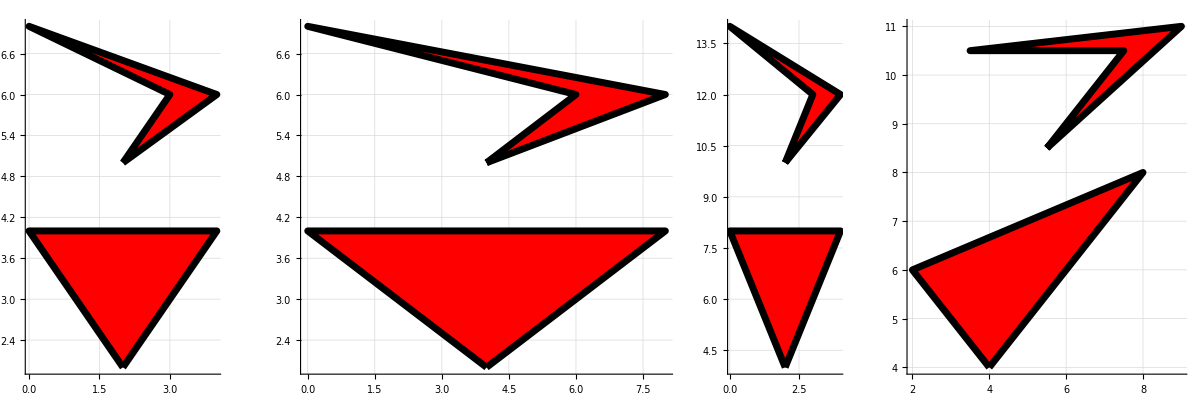

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
GraphicsRow[
{fig12//toGL//gr1,
sca3[fig12,{2,{1,0}}]//toGL//gr1,
sca3[fig12,{2,{0,1}}]//toGL//gr1,
sca3[fig12,{2,{1,1}}]//toGL//gr1}
]
```

## Property Updates

### FACE COLOR

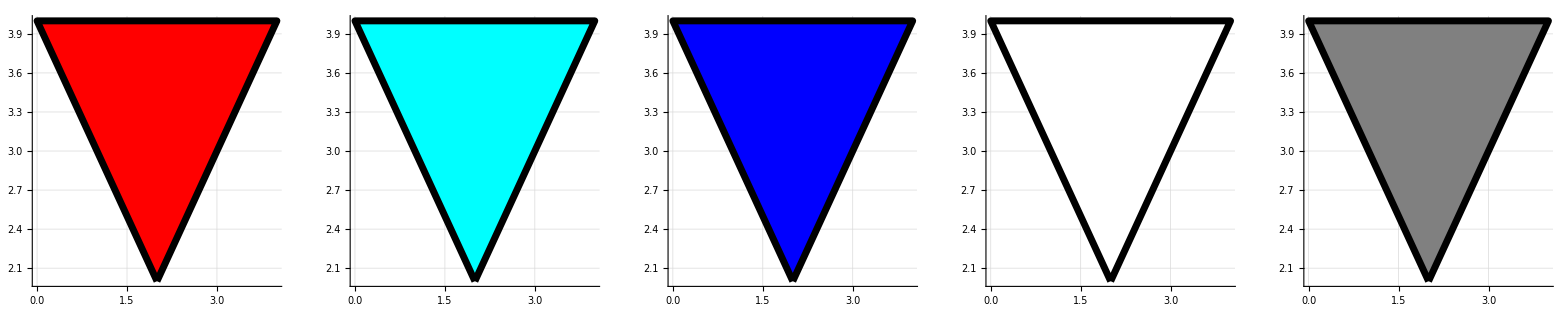

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
GraphicsRow[
{fig1//toGL//gr1,
repCol[fig1,{Cyan}]//toGL//gr1,
repCol[fig1,{Blue}]//toGL//gr1,
repCol[fig1,{White}]//toGL//gr1,
repCol[fig1,{Gray}]//toGL//gr1
}
]
```

### LINE COLOR

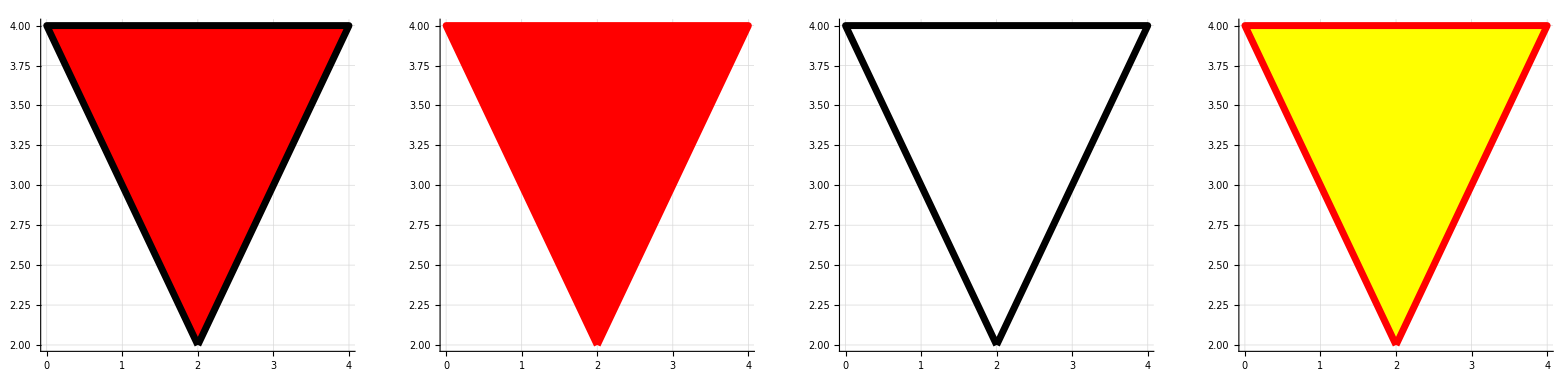

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
GraphicsRow[
{fig1//toGL//gr1,
repLineCol[fig1,{Red}]//toGL//gr1,
repCol[fig1,{White}]//toGL//gr1,
repLineCol[repCol[fig1,{Yellow}],{Red}]//toGL//gr1
}
]
```

## KNOWN BUGS

### BUG-1

```mathematica
Manipulate[
gHLinePD[p,q,Color->Blue,Thickness->0.0075]//grD
,
{{p,{0.4,0.2}},{-1,-1},{2,2},{0.1,0.1},Locator},
{{q,{-0.4,-0.2}},{-1,-1},{2,2},{0.1,0.1},Locator}
]
```

### BUG-2

```mathematica
Manipulate[
gHLinePD[p,q,Thickness->0.0075,Color->Blue]//toGL//grD
,
{{p,{0.6,-0.2}},{-1,-1},{2,2},{0.1,0.1},Locator},
{{q,{0.4,0.4}},{-1,-1},{2,2},{0.1,0.1},Locator}
]
```